```mathematica
(*Simulate result on 16^4 sites lattice with Z2 and Z6  *)
```

```mathematica
xcyc={0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.06500001,0.066,0.067,0.068,0.06900001,0.07,0.071,0.072,0.07300001,0.074,0.075,0.07600001,0.077,0.078,0.079,0.08000001,0.081,0.082,0.083,0.08400001,0.085,0.086,0.087,0.08800001,0.089,0.09,0.09100001,0.092,0.093,0.094,0.09500001,0.096,0.097,0.098,0.09900001,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3,0.301,0.302,0.303,0.304,0.305,0.306,0.307,0.308,0.309,0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32,0.321,0.322,0.323,0.324,0.325,0.326,0.327,0.328,0.329,0.33,0.331,0.332,0.333,0.334,0.335,0.336,0.337,0.338,0.339,0.34,0.341,0.342,0.343,0.344,0.345,0.346,0.347,0.348,0.349,0.35,0.351,0.352,0.353,0.354,0.355,0.356,0.357,0.358,0.359,0.36,0.361,0.362,0.363,0.364,0.365,0.366,0.367,0.368,0.369,0.37,0.371,0.372,0.373,0.374,0.375,0.376,0.377,0.378,0.379,0.38,0.381,0.382,0.383,0.384,0.385,0.386,0.387,0.388,0.389,0.39,0.391,0.392,0.393,0.394,0.395,0.396,0.397,0.398,0.399,0.4,0.401,0.402,0.403,0.404,0.405,0.406,0.407,0.408,0.409,0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417,0.418,0.419,0.42,0.421,0.422,0.423,0.424,0.425,0.426,0.427,0.428,0.429,0.43,0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439,0.44,0.441,0.442,0.443,0.444,0.445,0.446,0.447,0.448,0.449,0.45,0.451,0.452,0.453,0.454,0.455,0.456,0.457,0.458,0.459,0.46,0.461,0.462,0.463,0.464,0.465,0.466,0.467,0.468,0.469,0.47,0.471,0.472,0.473,0.474,0.475,0.476,0.477,0.478,0.479,0.48,0.481,0.482,0.483,0.484,0.485,0.486,0.487,0.488,0.489,0.49,0.491,0.492,0.493,0.494,0.495,0.496,0.497,0.498,0.499,0.5,0.501,0.502,0.503,0.504,0.505,0.506,0.507,0.508,0.509,0.5100001,0.511,0.512,0.513,0.514,0.515,0.516,0.517,0.518,0.5190001,0.52,0.521,0.522,0.523,0.524,0.525,0.526,0.527,0.528,0.529,0.53,0.531,0.532,0.5330001,0.534,0.535,0.536,0.537,0.538,0.539,0.54,0.541,0.542,0.543,0.544,0.545,0.546,0.5470001,0.548,0.549,0.55,0.551,0.552,0.553,0.554,0.555,0.5560001,0.557,0.558,0.559,0.56,0.561,0.562,0.563,0.564,0.565,0.566,0.567,0.568,0.569,0.5700001,0.571,0.572,0.573,0.574,0.575,0.576,0.577,0.578,0.5790001,0.58,0.581,0.582,0.583,0.5840001,0.585,0.586,0.587,0.588,0.589,0.59,0.591,0.592,0.5930001,0.594,0.595,0.596,0.597,0.598,0.599,0.6,0.601,0.602,0.603,0.604,0.605,0.606,0.6070001,0.608,0.609,0.61,0.611,0.612,0.613,0.614,0.615,0.6160001,0.617,0.618,0.619,0.62,0.6210001,0.622,0.623,0.624,0.625,0.626,0.627,0.628,0.629,0.6300001,0.631,0.632,0.633,0.634,0.6350001,0.636,0.637,0.638,0.6390001,0.64,0.641,0.642,0.643,0.6440001,0.645,0.646,0.647,0.648,0.649,0.65,0.651,0.652,0.6530001,0.654,0.655,0.656,0.657,0.6580001,0.659,0.66,0.661,0.6620001,0.663,0.664,0.665,0.666,0.6670001,0.668,0.669,0.67,0.671,0.6720001,0.673,0.674,0.675,0.6760001,0.677,0.678,0.679,0.68,0.6810001,0.682,0.683,0.684,0.685,0.686,0.687,0.688,0.689,0.6900001,0.691,0.692,0.693,0.694,0.6950001,0.696,0.697,0.698,0.6990001,0.7,0.701,0.702,0.703,0.7040001,0.705,0.706,0.707,0.708,0.7090001,0.71,0.711,0.712,0.7130001,0.714,0.715,0.716,0.717,0.7180001,0.719,0.72,0.721,0.7220001,0.723,0.724,0.725,0.726,0.7270001,0.728,0.729,0.73,0.731,0.7320001,0.733,0.734,0.735,0.7360001,0.737,0.738,0.739,0.74,0.7410001,0.742,0.743,0.744,0.7450001,0.7460001,0.747,0.748,0.749,0.7500001,0.751,0.752,0.753,0.754,0.7550001,0.756,0.757,0.758,0.7590001,0.7600001,0.761,0.762,0.763,0.7640001,0.765,0.766,0.767,0.768,0.7690001,0.77,0.771,0.772,0.7730001,0.774,0.775,0.776,0.777,0.7780001,0.779,0.78,0.781,0.7820001,0.7830001,0.784,0.785,0.786,0.7870001,0.788,0.789,0.79,0.791,0.7920001,0.793,0.794,0.795,0.7960001,0.7970001,0.798,0.799,0.8,0.8010001,0.802,0.803,0.804,0.8050001,0.8060001,0.807,0.808,0.809,0.8100001,0.811,0.812,0.813,0.814,0.8150001,0.816,0.817,0.818,0.8190001,0.8200001,0.821,0.822,0.823,0.8240001,0.825,0.826,0.827,0.828,0.8290001,0.83,0.831,0.832,0.8330001,0.8340001,0.835,0.836,0.837,0.8380001,0.839,0.84,0.841,0.8420001,0.8430001,0.844,0.845,0.846,0.8470001,0.848,0.849,0.85,0.851,0.8520001,0.853,0.854,0.855,0.8560001,0.8570001,0.858,0.859,0.86,0.8610001,0.862,0.863,0.864,0.8650001,0.8660001,0.867,0.868,0.869,0.8700001,0.8710001,0.872,0.873,0.874,0.8750001,0.876,0.877,0.878,0.8790001,0.8800001,0.881,0.882,0.883,0.8840001,0.8850001,0.886,0.887,0.8880001,0.8890001,0.89,0.891,0.892,0.8930001,0.8940001,0.895,0.896,0.897,0.8980001,0.899,0.9,0.901,0.9020001,0.9030001,0.904,0.905,0.906,0.9070001,0.9080001,0.909,0.91,0.911,0.9120001,0.913,0.914,0.915,0.9160001,0.9170001,0.918,0.919,0.92,0.9210001,0.9220001,0.923,0.924,0.9250001,0.9260001,0.927,0.928,0.929,0.9300001,0.9310001,0.932,0.933,0.934,0.9350001,0.936,0.937,0.938,0.9390001,0.9400001,0.941,0.942,0.943,0.9440001,0.9450001,0.946,0.947,0.9480001,0.9490001,0.95,0.951,0.952,0.9530001,0.9540001,0.955,0.956,0.957,0.9580001,0.9590001,0.96,0.961,0.9620001,0.9630001,0.964,0.965,0.966,0.9670001,0.9680001,0.969,0.97,0.971,0.9720001,0.973,0.974,0.975,0.9760001,0.9770001,0.978,0.979,0.98,0.9810001,0.9820001,0.983,0.984,0.9850001,0.9860001,0.987,0.988,0.989,0.9900001,0.9910001,0.992,0.993,0.994,0.9950001,0.9960001,0.997,0.998,0.9990001,1};
```

```mathematica
ycyc={1.002533,0.998646,1.000199,0.9978287,0.9974913,1.000171,0.9984668,0.9973466,0.9978896,0.9931867,0.9968757,0.9944148,0.9946218,0.9969003,0.9988247,0.9971668,0.9923149,0.9934966,0.9932075,0.9925331,0.9927609,0.9927442,0.9922648,0.9923057,0.9901378,0.9919856,0.9914486,0.989391,0.9860122,0.9947212,0.9873556,0.9909877,0.9901612,0.9902865,0.9914243,0.9863123,0.9881377,0.9901315,0.9916068,0.9869994,0.989547,0.9874322,0.9847579,0.983164,0.989408,0.9866487,0.9806805,0.9857288,0.9829624,0.9870414,0.9824923,0.98101,0.986941,0.9816782,0.9841954,0.983051,0.9848188,0.9808623,0.9877313,0.9815856,0.9820804,0.9803047,0.9821385,0.9814932,0.976754,0.9814627,0.9738697,0.9796182,0.9827628,0.9847864,0.9779568,0.9810913,0.9814702,0.9863474,0.9776854,0.9753991,0.9816757,0.9826451,0.9791778,0.9786725,0.973699,0.9763116,0.9741768,0.9803318,0.9825562,0.9779486,0.9751099,0.9700292,0.9680533,0.9737852,0.9760618,0.9828296,0.9754286,0.96519,0.9672713,0.9726211,0.9730592,0.9757005,0.972,0.9754312,0.9727649,0.9672415,0.9710848,0.9686223,0.972371,0.9765449,0.9730945,0.9600843,0.971959,0.9666516,0.9688273,0.9754062,0.96592,0.9716318,0.9733062,0.9655458,0.9679059,0.96196,0.9599902,0.9647576,0.9686009,0.9576651,0.9590511,0.9709306,0.9549747,0.9689345,0.9560568,0.969814,0.973857,0.9698874,0.9669673,0.9679261,0.9480887,0.9531931,0.9659321,0.9537467,0.9608837,0.9669948,0.9738679,0.9570504,0.9469511,0.9588765,0.973459,0.9642807,0.9537606,0.9656585,0.9413184,0.96117,0.9540221,0.9473462,0.9710841,0.9666698,0.9630294,0.9491832,0.9639262,0.9473776,0.9552045,0.9622979,0.9529501,0.9355353,0.9484453,0.9626983,0.9633776,0.9567965,0.9642702,0.9574261,0.9539826,0.9351771,0.9488599,0.9486305,0.942044,0.9548128,0.9483767,0.9550074,0.9390466,0.9578158,0.9371988,0.9546642,0.9426039,0.9596866,0.9478232,0.9452586,0.9325318,0.9474294,0.9434436,0.9567439,0.9306347,0.9563549,0.9534896,0.9533706,0.9290729,0.9474514,0.9307229,0.9433938,0.940133,0.9259149,0.9504455,0.9389753,0.9102114,0.9302967,0.9214613,0.9626979,0.9237113,0.9301509,0.9535902,0.9394302,0.9269221,0.9435349,0.929399,0.945276,0.9253085,0.9146212,0.8996961,0.9401147,0.9190389,0.9134321,0.9277633,0.9402363,0.8952636,0.93446,0.9384257,0.9157227,0.9226536,0.9218279,0.9124079,0.9393922,0.9156833,0.8988926,0.9261132,0.9226395,0.9359109,0.9199796,0.9082814,0.9002177,0.9080389,0.9328415,0.9116517,0.8909001,0.8808486,0.8931594,0.8756507,0.9083279,0.9199235,0.9048377,0.8625404,0.8857945,0.8999463,0.8768759,0.9068468,0.8979061,0.9165958,0.8484416,0.8947726,0.8647175,0.9292648,0.8719658,0.8574471,0.8984436,0.8969244,0.8431663,0.8938614,0.881315,0.8427763,0.8612045,0.884632,0.8654063,0.9010915,0.8823266,0.8721907,0.8945013,0.8787449,0.8684893,0.8478826,0.8300961,0.8796616,0.8643149,0.8195392,0.8908903,0.8108225,0.8998451,0.8586959,0.8517276,0.8087716,0.8063292,0.9094988,0.8564171,0.7925907,0.7819477,0.8704787,0.8856091,0.8225567,0.8314334,0.8649535,0.7697777,0.7700366,0.7482219,0.8181169,0.7971193,0.8697779,0.6730347,0.8471887,0.7301151,0.7676522,0.7303383,0.7136476,0.7986587,0.8956885,0.825271,0.8701194,0.7897018,0.8668262,0.6357943,0.7364268,0.7212932,0.6360616,0.6901095,0.6692858,0.7382592,0.5149349,0.7264563,0.7332558,0.7116013,0.6945391,0.8181257,0.7226731,0.5866978,0.6635485,0.8457238,0.6189127,0.7900768,0.5710266,0.7537763,0.6633356,0.4394771,0.655147,0.825206,0.4560499,0.6901644,0.5930043,0.6865769,0.677033,0.4816335,0.3518337,0.1954395,0.5174099,0.5056471,0.5243934,0.5952805,0.5260597,0.699824,0.6329128,0.5185909,0.2466417,0.64692,0.3586303,0.4265969,0.6002297,0.5224681,0.5163243,0.3691183,0.379109,0.5487776,0.3849652,0.6338229,0.3759358,0.2009158,0.4646833,0.3194037,0.4391885,0.3448613,0.3871526,0.2357573,0.2674826,0.406804,0.4417802,0.3445435,0.1128342,0.2002756,0.4104727,0.2418405,0.2650637,0.1705305,0.19279,0.1241397,0.5077547,0.6058738,0.2383398,0.1171025,0.4133383,0.3839694,0.3173299,0.3697781,0.3366354,0.4705707,0.27503,0.2424525,0.2373468,0.1893281,0.4030527,0.2717195,0.123629,0.2017999,0.277351,0.169098,0.1043661,0.1183882,0.1998745,0.2564203,0.06400812,0.1135213,0.05878318,0.1230513,0.154297,0.08206003,0.1786023,0.05747097,0.228094,0.083007,0.0957697,0.3328643,0.1669369,0.1624464,0.05843124,0.07573891,0.2155812,0.1476663,0.1148093,0.07834749,0.06846603,0.2642705,0.04131224,0.1765785,0.06745901,0.07479249,0.05391126,0.09072971,0.1014793,0.158159,0.07548822,0.04929473,0.1045613,0.09782022,0.09630773,0.1591341,0.1341517,0.1614847,0.2329948,0.1788804,0.08171277,0.1035382,0.2419761,0.09581225,0.05833121,0.05718249,0.07746756,0.03098572,0.1172972,0.05352757,0.1550458,0.2007348,0.0954113,0.08592891,0.09645307,0.2451674,0.06740331,0.05034932,0.07426032,0.07194706,0.04998349,0.05901941,0.08493813,0.06903879,0.0880999,0.1225486,0.06891531,0.1038735,0.101035,0.05392287,0.1258599,0.05725672,0.1861749,0.08878417,0.02117021,0.04256827,0.07178474,0.07097689,0.05090019,0.1779474,0.05265648,0.02952384,0.02367761,0.02571645,0.05434793,0.04196847,0.02155908,0.04354906,0.0245874,0.0309976,0.05650277,0.04853648,0.02123706,0.02905878,0.04178141,0.02746791,0.02139954,0.03818119,0.04054379,0.08436275,0.08646852,0.05427768,0.05486167,0.03899192,0.03365213,0.04213289,0.05516536,0.1128125,0.03977805,0.0341015,0.0423621,0.07813228,0.04581711,0.05565762,0.02523534,0.02603436,0.02213076,0.02018708,0.01852674,0.09054288,0.07421779,0.03523705,0.06418923,0.05772065,0.03224713,0.02241136,0.02521321,0.0832721,0.03376103,0.02172363,0.0322214,0.04663491,0.02600234,0.06504885,0.04066465,0.0570831,0.0445399,0.05154195,0.05125145,0.04362677,0.02461424,0.05896774,0.04783286,0.01830647,0.05192493,0.02459903,0.01960535,0.03703364,0.04562129,0.1041514,0.04538485,0.09021021,0.02830128,0.04554668,0.08509759,0.04073523,0.0178626,0.0771677,0.02182493,0.02421656,0.04282399,0.03541892,0.03207468,0.08079644,0.01704188,0.0347767,0.02720038,0.02841109,0.06683856,0.05639916,0.07928366,0.03615784,0.0357347,0.02095624,0.02801073,0.06593343,0.02066491,0.02608225,0.01719688,0.02775941,0.03936329,0.02016172,0.01723571,0.06816565,0.02388751,0.04164806,0.03424631,0.01679366,0.03811026,0.05820389,0.0308922,0.06210549,0.01700343,0.02729835,0.0169115,0.06407068,0.04600573,0.01635387,0.08117112,0.01684661,0.05089702,0.03167948,0.01716757,0.02007425,0.0886068,0.02621269,0.0273713,0.0776415,0.02863322,0.04371656,0.05013031,0.02856735,0.03672345,0.0235427,0.07142088,0.01632441,0.04110265,0.05039719,0.01637963,0.04149759,0.05919614,0.06067269,0.02104376,0.02996952,0.01975749,0.03253086,0.04190343,0.01617885,0.02444143,0.04496972,0.01948804,0.01956036,0.04849072,0.03995202,0.03548867,0.02290271,0.03623179,0.02328695,0.01612068,0.01635372,0.01955452,0.01619698,0.03530375,0.02821091,0.02875438,0.03145745,0.0417797,0.03856996,0.02282141,0.03703595,0.01638854,0.0434941,0.0160076,0.06670712,0.02020757,0.02608284,0.02687878,0.01959563,0.01598728,0.01605361,0.03704665,0.01628302,0.02807972,0.02775161,0.01607914,0.01931425,0.01627478,0.0162003,0.0415513,0.0303035,0.03958762,0.07316733,0.05680593,0.01611456,0.0198218,0.04328042,0.09187926,0.06133889,0.0511214,0.03136474,0.01566806,0.01592942,0.04526213,0.02736765,0.03165121,0.04109071,0.02468827,0.01950463,0.03145952,0.0189487,0.03293902,0.03656819,0.01573929,0.01588515,0.04210323,0.03749581,0.02247761,0.02850808,0.02727806,0.01568959,0.0302611,0.04485797,0.05375069,0.01965657,0.01579474,0.03314073,0.02267738,0.02840285,0.02582361,0.02680383,0.01923907,0.01567259,0.03618345,0.03032324,0.01575009,0.0529658,0.02443033,0.03590071,0.03673002,0.0422469,0.03724175,0.02656724,0.01890539,0.02985095,0.05671795,0.0156457,0.02791986,0.0500454,0.02629039,0.03379532,0.06386695,0.01567183,0.03236293,0.05614592,0.01901008,0.03792723,0.02032118,0.01914679,0.0546948,0.01573264,0.02630467,0.06301641,0.02837498,0.01574057,0.04067892,0.02899878,0.03084063,0.02924402,0.0388698,0.02832477,0.01563452,0.01569125,0.015667,0.03660088,0.02646342,0.02597877,0.02999624,0.02599224,0.04861619,0.01570696,0.04683028,0.03168666,0.04753256,0.03412523,0.04948042,0.02423116,0.04003184,0.02803009,0.01571376,0.03300526,0.02740529,0.02345953,0.0355485,0.01559388,0.01562787,0.01560959,0.01541349,0.02307625,0.03737726,0.02393953,0.01550754,0.04765587,0.02825135,0.01564487,0.04346277,0.06301767,0.01535888,0.02852235,0.02752809,0.02773109,0.05542105,0.02834343,0.02962655,0.01569706,0.05380904,0.01556419,0.02904017,0.01553458,0.02931624,0.01543729,0.02202219,0.04379187,0.03623776,0.01556495,0.01555248,0.015411,0.0291499,0.02739972,0.0598637,0.0153832,0.03570179,0.01548034,0.02235672,0.01548767,0.01555966,0.01880543,0.0388412,0.01552536,0.01547808,0.02551829,0.02492395,0.01543275,0.02451131,0.02500946,0.01565476,0.01537142,0.03027044,0.02886036,0.06443719,0.02602079,0.03743827,0.0427377,0.07125192,0.01553957,0.02551045,0.023777,0.04328802,0.03091365,0.01553828,0.02657084,0.01586068,0.01558021,0.02767763,0.02416373,0.03030942,0.01554357,0.02815806,0.01874842,0.04017835,0.03005939,0.02599287,0.01536515,0.01546085,0.01540035,0.02851135,0.02281486,0.02652856,0.05470316,0.02206451,0.06246815,0.02300391,0.02273303,0.02204918,0.03949735,0.0411142,0.03539332,0.02769722,0.04501195,0.01552302,0.0375304,0.02372608,0.02679197,0.0453493,0.04112259,0.02656492,0.02435278,0.05191282,0.03506948,0.0154882,0.01542482,0.01551585,0.03752678,0.04111931,0.01538728,0.02171396,0.04671076,0.0293079,0.04512732,0.03551876,0.04772176,0.03403145,0.02664807,0.02669601,0.02877206,0.0236134,0.02516756,0.01562296,0.06456172,0.02684343,0.02197762,0.015302,0.02195196,0.02269423,0.02508079,0.02874393,0.03312978,0.02738089,0.03188108,0.02877941,0.02518337,0.01534989,0.02731175,0.03517742,0.01558572,0.01553518,0.04037581,0.05380601,0.06475107,0.01524232,0.02553981,0.04498646,0.0588454,0.05075234,0.06116647,0.02783843,0.01560755,0.01547264,0.02556862,0.02624471,0.03141085,0.03219783,0.02473561,0.04116968,0.01550701,0.03683968,0.02254811,0.01543517,0.01527722,0.02640622,0.01556563,0.01527103,0.01542324,0.01541168,0.03436315,0.04002051,0.04231081,0.01543321,0.01547438,0.0265928,0.02689329,0.01526634,0.01553156,0.01537791,0.01550399,0.02938264,0.04344804,0.03695802,0.0202433,0.04070466,0.01549832,0.02632834,0.0315893,0.04895914,0.01547951,0.02532705,0.01537013,0.01554553,0.04281938,0.02378082,0.02382383,0.02630298,0.01558814,0.01547709,0.02465944,0.05038344,0.01547709,0.02867049,0.05258917,0.03725249,0.02289206,0.01533946,0.02869569,0.02504365};
```

```mathematica
xcyc2={1,0.9990001,0.998,0.997,0.9960001,0.9950001,0.994,0.993,0.992,0.9910001,0.9900001,0.989,0.988,0.987,0.9860001,0.9850001,0.984,0.983,0.9820001,0.9810001,0.98,0.979,0.978,0.9770001,0.9760001,0.975,0.974,0.973,0.9720001,0.971,0.97,0.969,0.9680001,0.9670001,0.966,0.965,0.964,0.9630001,0.9620001,0.961,0.96,0.9590001,0.9580001,0.957,0.956,0.955,0.9540001,0.9530001,0.952,0.951,0.95,0.9490001,0.9480001,0.947,0.946,0.9450001,0.9440001,0.943,0.942,0.941,0.9400001,0.9390001,0.938,0.937,0.936,0.9350001,0.934,0.933,0.932,0.9310001,0.9300001,0.929,0.928,0.927,0.9260001,0.9250001,0.924,0.923,0.9220001,0.9210001,0.92,0.919,0.918,0.9170001,0.9160001,0.915,0.914,0.913,0.9120001,0.911,0.91,0.909,0.9080001,0.9070001,0.906,0.905,0.904,0.9030001,0.9020001,0.901,0.9,0.899,0.8980001,0.897,0.896,0.895,0.8940001,0.8930001,0.892,0.891,0.89,0.8890001,0.8880001,0.887,0.886,0.8850001,0.8840001,0.883,0.882,0.881,0.8800001,0.8790001,0.878,0.877,0.876,0.8750001,0.874,0.873,0.872,0.8710001,0.8700001,0.869,0.868,0.867,0.8660001,0.8650001,0.864,0.863,0.862,0.8610001,0.86,0.859,0.858,0.8570001,0.8560001,0.855,0.854,0.853,0.8520001,0.851,0.85,0.849,0.848,0.8470001,0.846,0.845,0.844,0.8430001,0.8420001,0.841,0.84,0.839,0.8380001,0.837,0.836,0.835,0.8340001,0.8330001,0.832,0.831,0.83,0.8290001,0.828,0.827,0.826,0.825,0.8240001,0.823,0.822,0.821,0.8200001,0.8190001,0.818,0.817,0.816,0.8150001,0.814,0.813,0.812,0.811,0.8100001,0.809,0.808,0.807,0.8060001,0.8050001,0.804,0.803,0.802,0.8010001,0.8,0.799,0.798,0.7970001,0.7960001,0.795,0.794,0.793,0.7920001,0.791,0.79,0.789,0.788,0.7870001,0.786,0.785,0.784,0.7830001,0.7820001,0.781,0.78,0.779,0.7780001,0.777,0.776,0.775,0.774,0.7730001,0.772,0.771,0.77,0.7690001,0.768,0.767,0.766,0.765,0.7640001,0.763,0.762,0.761,0.7600001,0.7590001,0.758,0.757,0.756,0.7550001,0.754,0.753,0.752,0.751,0.7500001,0.749,0.748,0.747,0.7460001,0.7450001,0.744,0.743,0.742,0.7410001,0.74,0.739,0.738,0.737,0.7360001,0.735,0.734,0.733,0.7320001,0.731,0.73,0.729,0.728,0.7270001,0.726,0.725,0.724,0.723,0.7220001,0.721,0.72,0.719,0.7180001,0.717,0.716,0.715,0.714,0.7130001,0.712,0.711,0.71,0.7090001,0.708,0.707,0.706,0.705,0.7040001,0.703,0.702,0.701,0.7,0.6990001,0.698,0.697,0.696,0.6950001,0.694,0.693,0.692,0.691,0.6900001,0.689,0.688,0.687,0.686,0.685,0.684,0.683,0.682,0.6810001,0.68,0.679,0.678,0.677,0.6760001,0.675,0.674,0.673,0.6720001,0.671,0.67,0.669,0.668,0.6670001,0.666,0.665,0.664,0.663,0.6620001,0.661,0.66,0.659,0.6580001,0.657,0.656,0.655,0.654,0.6530001,0.652,0.651,0.65,0.649,0.648,0.647,0.646,0.645,0.6440001,0.643,0.642,0.641,0.64,0.6390001,0.638,0.637,0.636,0.6350001,0.634,0.633,0.632,0.631,0.6300001,0.629,0.628,0.627,0.626,0.625,0.624,0.623,0.622,0.6210001,0.62,0.619,0.618,0.617,0.6160001,0.615,0.614,0.613,0.612,0.611,0.61,0.609,0.608,0.6070001,0.606,0.605,0.604,0.603,0.602,0.601,0.6,0.599,0.598,0.597,0.596,0.595,0.594,0.5930001,0.592,0.591,0.59,0.589,0.588,0.587,0.586,0.585,0.5840001,0.583,0.582,0.581,0.58,0.5790001,0.578,0.577,0.576,0.575,0.574,0.573,0.572,0.571,0.5700001,0.569,0.568,0.567,0.566,0.565,0.564,0.563,0.562,0.561,0.56,0.559,0.558,0.557,0.5560001,0.555,0.554,0.553,0.552,0.551,0.55,0.549,0.548,0.5470001,0.546,0.545,0.544,0.543,0.542,0.541,0.54,0.539,0.538,0.537,0.536,0.535,0.534,0.5330001,0.532,0.531,0.53,0.529,0.528,0.527,0.526,0.525,0.524,0.523,0.522,0.521,0.52,0.5190001,0.518,0.517,0.516,0.515,0.514,0.513,0.512,0.511,0.5100001,0.509,0.508,0.507,0.506,0.505,0.504,0.503,0.502,0.501,0.5,0.499,0.498,0.497,0.496,0.495,0.494,0.493,0.492,0.491,0.49,0.489,0.488,0.487,0.486,0.485,0.484,0.483,0.482,0.481,0.48,0.479,0.478,0.477,0.476,0.475,0.474,0.473,0.472,0.471,0.47,0.469,0.468,0.467,0.466,0.465,0.464,0.463,0.462,0.461,0.46,0.459,0.458,0.457,0.456,0.455,0.454,0.453,0.452,0.451,0.45,0.449,0.448,0.447,0.446,0.445,0.444,0.443,0.442,0.441,0.44,0.439,0.438,0.437,0.436,0.435,0.434,0.433,0.432,0.431,0.43,0.429,0.428,0.427,0.426,0.425,0.424,0.423,0.422,0.421,0.42,0.419,0.418,0.417,0.416,0.415,0.414,0.413,0.412,0.411,0.41,0.409,0.408,0.407,0.406,0.405,0.404,0.403,0.402,0.401,0.4,0.399,0.398,0.397,0.396,0.395,0.394,0.393,0.392,0.391,0.39,0.389,0.388,0.387,0.386,0.385,0.384,0.383,0.382,0.381,0.38,0.379,0.378,0.377,0.376,0.375,0.374,0.373,0.372,0.371,0.37,0.369,0.368,0.367,0.366,0.365,0.364,0.363,0.362,0.361,0.36,0.359,0.358,0.357,0.356,0.355,0.354,0.353,0.352,0.351,0.35,0.349,0.348,0.347,0.346,0.345,0.344,0.343,0.342,0.341,0.34,0.339,0.338,0.337,0.336,0.335,0.334,0.333,0.332,0.331,0.33,0.329,0.328,0.327,0.326,0.325,0.324,0.323,0.322,0.321,0.32,0.319,0.318,0.317,0.316,0.315,0.314,0.313,0.312,0.311,0.31,0.309,0.308,0.307,0.306,0.305,0.304,0.303,0.302,0.301,0.3,0.299,0.298,0.297,0.296,0.295,0.294,0.293,0.292,0.291,0.29,0.289,0.288,0.287,0.286,0.285,0.284,0.283,0.282,0.281,0.28,0.279,0.278,0.277,0.276,0.275,0.274,0.273,0.272,0.271,0.27,0.269,0.268,0.267,0.266,0.265,0.264,0.263,0.262,0.261,0.26,0.259,0.258,0.257,0.256,0.255,0.254,0.253,0.252,0.251,0.25,0.249,0.248,0.247,0.246,0.245,0.244,0.243,0.242,0.241,0.24,0.239,0.238,0.237,0.236,0.235,0.234,0.233,0.232,0.231,0.23,0.229,0.228,0.227,0.226,0.225,0.224,0.223,0.222,0.221,0.22,0.219,0.218,0.217,0.216,0.215,0.214,0.213,0.212,0.211,0.21,0.209,0.208,0.207,0.206,0.205,0.204,0.203,0.202,0.201,0.2,0.199,0.198,0.197,0.196,0.195,0.194,0.193,0.192,0.191,0.19,0.189,0.188,0.187,0.186,0.185,0.184,0.183,0.182,0.181,0.18,0.179,0.178,0.177,0.176,0.175,0.174,0.173,0.172,0.171,0.17,0.169,0.168,0.167,0.166,0.165,0.164,0.163,0.162,0.161,0.16,0.159,0.158,0.157,0.156,0.155,0.154,0.153,0.152,0.151,0.15,0.149,0.148,0.147,0.146,0.145,0.144,0.143,0.142,0.141,0.14,0.139,0.138,0.137,0.136,0.135,0.134,0.133,0.132,0.131,0.13,0.129,0.128,0.127,0.126,0.125,0.124,0.123,0.122,0.121,0.12,0.119,0.118,0.117,0.116,0.115,0.114,0.113,0.112,0.111,0.11,0.109,0.108,0.107,0.106,0.105,0.104,0.103,0.102,0.101,0.1,0.09900001,0.098,0.097,0.096,0.09500001,0.094,0.093,0.092,0.09100001,0.09,0.089,0.08800001,0.087,0.086,0.085,0.08400001,0.083,0.082,0.081,0.08000001,0.079,0.078,0.077,0.07600001,0.075,0.074,0.07300001,0.072,0.071,0.07,0.06900001,0.068,0.067,0.066,0.06500001,0.064,0.063,0.062,0.061,0.06,0.059,0.058,0.057,0.056,0.055,0.054,0.053,0.052,0.051,0.05,0.049,0.048,0.047,0.046,0.045,0.044,0.043,0.042,0.041,0.04,0.039,0.038,0.037,0.036,0.035,0.034,0.033,0.032,0.031,0.03,0.029,0.028,0.027,0.026,0.025,0.024,0.023,0.022,0.021,0.02,0.019,0.018,0.017,0.016,0.015,0.014,0.013,0.012,0.011,0.01};
ycyc2={0.02504365,0.01532549,0.04046523,0.01533629,0.06647021,0.02290735,0.01547362,0.02793169,0.02923841,0.0290959,0.01531514,0.0366138,0.01531084,0.02540342,0.03717711,0.03854725,0.02342992,0.01541818,0.04714878,0.01535578,0.02823501,0.02877098,0.03174657,0.05773778,0.0153233,0.07506213,0.03153402,0.01539823,0.0302152,0.04205103,0.01546048,0.02864657,0.0154388,0.03153586,0.05463171,0.02628113,0.03770278,0.02174723,0.04569058,0.03648873,0.03659546,0.03057886,0.01532458,0.03209399,0.01541349,0.04797849,0.03108017,0.02558053,0.02872573,0.01536024,0.03535336,0.01539921,0.01540987,0.05192888,0.01549137,0.04136308,0.05528083,0.01542762,0.0252254,0.01535555,0.03484846,0.01536809,0.01539853,0.01540405,0.01560687,0.03680752,0.01539529,0.04379253,0.05120492,0.01553367,0.06639603,0.03067908,0.04437724,0.03104582,0.025019,0.0153943,0.01562288,0.02206038,0.02896566,0.01563588,0.02837067,0.02723714,0.06475677,0.04043073,0.02687289,0.01547845,0.02896209,0.02745341,0.03247891,0.02510703,0.01542671,0.028666,0.02873437,0.0272557,0.0153094,0.01544854,0.01540231,0.01558761,0.03030589,0.03952011,0.02816256,0.03375093,0.03116917,0.01550716,0.07748713,0.01555195,0.05462294,0.0217828,0.01540329,0.04131471,0.0548735,0.04748837,0.01541553,0.01551728,0.05151203,0.03191141,0.02187974,0.05024795,0.0152819,0.05519184,0.05526359,0.02511909,0.03922496,0.02897923,0.04645209,0.03558249,0.02738321,0.08097131,0.04046727,0.07204653,0.02768025,0.03357289,0.02786897,0.01526249,0.01537414,0.02565098,0.01546531,0.02213932,0.01550527,0.01534634,0.02621475,0.02677077,0.0500101,0.02642852,0.06487435,0.01559108,0.031871,0.06077485,0.02197651,0.02870745,0.03121759,0.05414169,0.01545791,0.0276868,0.03264948,0.03912804,0.01552703,0.01558149,0.0348515,0.03795951,0.01559169,0.03129613,0.02596673,0.04563793,0.05265932,0.03178909,0.02770631,0.0419287,0.0299906,0.04152639,0.01543721,0.03896767,0.01571988,0.04208248,0.01551131,0.02863083,0.0334979,0.03677665,0.03594095,0.01549069,0.02847023,0.0156173,0.02437292,0.04941864,0.01570764,0.02205582,0.01551003,0.01559569,0.03626337,0.02802108,0.02786534,0.03549776,0.02890078,0.05275271,0.02778862,0.03633128,0.03735898,0.01547196,0.03085561,0.01554251,0.02460996,0.01551917,0.01567886,0.02611131,0.02404534,0.02554417,0.02889161,0.04100971,0.02320884,0.08117132,0.01553375,0.02685041,0.02744908,0.03127435,0.03162036,0.02450267,0.01566745,0.015474,0.0366432,0.03499271,0.04962755,0.01552227,0.04130448,0.03545692,0.03176691,0.04618244,0.04023647,0.01572184,0.07951149,0.01564343,0.09374272,0.02589039,0.02428769,0.01577162,0.02802793,0.06536893,0.0247879,0.03584141,0.02826746,0.05983266,0.01587858,0.02559168,0.01609364,0.034069,0.03704391,0.05537659,0.0157584,0.02972868,0.02212001,0.02647211,0.01572365,0.01584195,0.01574646,0.03168223,0.01559584,0.01575749,0.03636842,0.02527248,0.01604492,0.0238402,0.05118334,0.02618189,0.01909073,0.02834708,0.02567389,0.08431104,0.04581806,0.03034392,0.04034051,0.02791696,0.01918632,0.0441337,0.03126322,0.07840389,0.01578461,0.03431659,0.02261937,0.01580697,0.05770121,0.04973156,0.02268207,0.05751571,0.04194059,0.05559465,0.02929003,0.01580901,0.02798588,0.03691829,0.02929353,0.03782966,0.03241951,0.0159582,0.04984772,0.04537107,0.02248146,0.02245087,0.02532559,0.06444362,0.03602897,0.01590495,0.04080578,0.02870838,0.04002355,0.03920545,0.01589581,0.04039621,0.03619153,0.05337802,0.03119846,0.02285646,0.04938031,0.01585517,0.02628268,0.04211793,0.0654763,0.03844051,0.06508613,0.06686069,0.05711405,0.03536509,0.0160774,0.03332459,0.04273393,0.04920438,0.02703825,0.02784407,0.0305525,0.04159022,0.04338172,0.06453086,0.02701256,0.01670837,0.02337161,0.0291701,0.01626126,0.01940097,0.04265023,0.05132352,0.05114308,0.01971335,0.04823875,0.01622228,0.01618127,0.04462216,0.01620702,0.04259521,0.01985252,0.03361053,0.05536,0.0383571,0.03023814,0.02264394,0.04206556,0.0161197,0.0309519,0.02921149,0.01616699,0.02313942,0.03057796,0.03561228,0.04001512,0.08314722,0.05571296,0.03255979,0.06020998,0.03411367,0.03494112,0.04276107,0.02718927,0.02925709,0.03817802,0.01979659,0.02720829,0.05389024,0.01633098,0.02540845,0.02341867,0.02737308,0.01665467,0.02706758,0.06061333,0.02509635,0.03003209,0.01642578,0.01667846,0.04596718,0.02889189,0.05314538,0.02724406,0.02014107,0.04777784,0.0237286,0.1105738,0.01691792,0.01665225,0.02353222,0.02066481,0.06192911,0.02787972,0.08923934,0.08419787,0.03618499,0.05718531,0.06177828,0.1310919,0.02404065,0.02734068,0.03770424,0.1045548,0.03045644,0.03059568,0.04289369,0.02042981,0.0235701,0.04129972,0.06876875,0.1117951,0.02055694,0.03235168,0.02369672,0.0173602,0.02778218,0.02725605,0.01743868,0.03079564,0.02180337,0.03906237,0.08036034,0.0176381,0.07175592,0.1035407,0.04549414,0.0465412,0.01844395,0.02520037,0.03832759,0.02079287,0.03409081,0.0413811,0.03700929,0.03900726,0.02447057,0.04390055,0.06790854,0.0441047,0.04936576,0.04666302,0.02150933,0.02135541,0.02958755,0.03297754,0.01890934,0.04336782,0.03005589,0.05533668,0.03732927,0.02946593,0.0579976,0.04480695,0.05676977,0.02392591,0.0357073,0.0339474,0.04243769,0.0698464,0.01919571,0.03806872,0.04607658,0.07383129,0.04425613,0.022136,0.01833955,0.03439719,0.04541396,0.08348844,0.05228117,0.04549156,0.02209808,0.05402419,0.07600823,0.05134925,0.01899938,0.04382002,0.02997247,0.02226824,0.1777888,0.1007953,0.02487482,0.05562166,0.04503873,0.03735943,0.07563389,0.04338688,0.04615973,0.0428636,0.04083534,0.04138806,0.03042436,0.03793088,0.06919798,0.03395871,0.08642226,0.1228222,0.03690597,0.04352061,0.02179824,0.02791495,0.04550659,0.05892031,0.04908121,0.07340983,0.1000906,0.03560462,0.08689012,0.06744533,0.07117842,0.05441521,0.2068132,0.1420146,0.07214879,0.0551859,0.04603156,0.1332047,0.08696401,0.05513013,0.183279,0.08171178,0.06970739,0.03783943,0.09083018,0.08377619,0.08822368,0.09471188,0.1265174,0.2080763,0.05890929,0.211996,0.1162906,0.1115437,0.08765472,0.06814424,0.09703853,0.1218456,0.1008102,0.05828132,0.1400519,0.1649687,0.09825623,0.114131,0.1562817,0.1810451,0.08861297,0.1059792,0.06816957,0.05537704,0.2528734,0.1060574,0.1586517,0.05462906,0.1462668,0.1276646,0.08055469,0.08253907,0.1205056,0.0645085,0.06684618,0.2681437,0.056065,0.04979638,0.09458946,0.07743379,0.06667134,0.1396119,0.1606287,0.1085863,0.2434975,0.1895021,0.2692795,0.1111294,0.07294504,0.1513562,0.4223034,0.1761115,0.1281414,0.08405747,0.07787456,0.1771203,0.4312654,0.4284827,0.2613078,0.5375286,0.1491455,0.1903164,0.12879,0.1007507,0.3085764,0.1751789,0.2989292,0.210298,0.3574359,0.2723076,0.183558,0.2628182,0.2069408,0.3374875,0.1965869,0.1203038,0.1576693,0.2180064,0.1909333,0.408081,0.1810694,0.2787214,0.4593622,0.3197646,0.3706438,0.3440887,0.3166971,0.3062946,0.2748895,0.3082762,0.4996536,0.318883,0.3581744,0.1890963,0.4092216,0.1131594,0.5543905,0.2453415,0.7480046,0.2500013,0.4235919,0.2743709,0.4713741,0.7311372,0.507663,0.4162763,0.3927341,0.4722201,0.6040035,0.2570707,0.4540606,0.7604339,0.7398465,0.4908646,0.472627,0.2418311,0.6517199,0.5841042,0.2999816,0.5728799,0.552344,0.4497554,0.7592191,0.6746057,0.5419595,0.6835092,0.6404572,0.6985376,0.5767509,0.61129,0.6794066,0.5525354,0.6753119,0.7169062,0.654497,0.6115313,0.6095325,0.7873511,0.7509536,0.7931536,0.7841752,0.781022,0.7333161,0.7643096,0.7213911,0.7961016,0.7683408,0.6822983,0.6492901,0.5986599,0.8639205,0.7933796,0.7578897,0.7489966,0.8013241,0.8160645,0.8464137,0.8202239,0.7501534,0.8230982,0.8577452,0.8380035,0.7996803,0.8195637,0.8866668,0.717186,0.7805145,0.8258601,0.7846627,0.820858,0.8040834,0.8178793,0.725421,0.741855,0.9145228,0.8980547,0.811657,0.8579549,0.784505,0.8467365,0.8577092,0.827116,0.8464051,0.8563656,0.8356358,0.8731571,0.8452131,0.841056,0.8698987,0.866151,0.8726795,0.9044067,0.8835294,0.8110455,0.8424625,0.8807215,0.8974949,0.8951626,0.8946514,0.8414293,0.8889892,0.8797938,0.8927814,0.8849212,0.8723426,0.8394222,0.8592198,0.8816284,0.9052449,0.8938681,0.8725403,0.9147305,0.920265,0.8831714,0.8979503,0.9166771,0.9291376,0.9013512,0.9023126,0.8785866,0.9084006,0.8837756,0.9363698,0.9001598,0.8961166,0.902519,0.8913541,0.9166356,0.8921666,0.9305632,0.8815079,0.9333835,0.9201339,0.9120064,0.928269,0.9055358,0.9090773,0.9181343,0.9237496,0.9062955,0.9231157,0.9223707,0.8845981,0.9123247,0.9117648,0.9539331,0.9253547,0.9266842,0.9181935,0.9131303,0.9387321,0.9127333,0.9387691,0.9305892,0.9533703,0.9286934,0.9168022,0.9235645,0.9556208,0.9532962,0.9139089,0.9320866,0.9361027,0.9475576,0.9320089,0.9261414,0.9320527,0.9449407,0.94438,0.9405501,0.9295109,0.9366883,0.9347287,0.9501069,0.9485663,0.9442645,0.9396857,0.9549739,0.9462764,0.9547104,0.9322753,0.9245779,0.9362277,0.9660621,0.938159,0.9476117,0.9371342,0.9440566,0.9339176,0.9364316,0.9488317,0.955098,0.938523,0.9568473,0.9499134,0.9447146,0.9540459,0.9702576,0.9499455,0.9485895,0.9680156,0.9587905,0.9566966,0.9544419,0.9547671,0.9543439,0.9572461,0.9519566,0.9708329,0.9713485,0.9537148,0.961022,0.9643865,0.9601053,0.9641483,0.9473172,0.9501793,0.9678847,0.9599022,0.9644102,0.9539369,0.9532304,0.9675092,0.9534823,0.9635556,0.9589098,0.966836,0.9647184,0.9662536,0.9504986,0.9613197,0.955859,0.9705193,0.9700223,0.9618844,0.9649982,0.9665303,0.9690197,0.968901,0.970382,0.9665618,0.9626736,0.9747054,0.960364,0.9671822,0.967555,0.9775956,0.9704009,0.965529,0.9667749,0.9671648,0.9698446,0.9683284,0.9721863,0.9599214,0.964879,0.9804292,0.9688249,0.981409,0.9906715,0.9582911,0.9811549,0.974333,0.9743906,0.9760857,0.9805423,0.9706159,0.9778387,0.9726182,0.9707125,0.9722022,0.9759681,0.9626938,0.9777465,0.9720722,0.9890606,0.9754914,0.9746555,0.9803225,0.9798964,0.9735993,0.9723569,0.9802433,0.9712598,0.9739496,0.9728919,0.983951,0.974,0.9804677,0.9746612,0.9825795,0.9826573,0.9758151,0.984005,0.9833332,0.9806324,0.9774512,0.9836619,0.9868927,0.9812813,0.9858112,0.9798347,0.9789969,0.9824185,0.9794214,0.9834434,0.9842046,0.9873255,0.9842219,0.9857565,0.9835681,0.996133,0.9809017,0.9848912,0.9852282,0.9859229,0.9812423,0.9824663,0.9861929,0.9870262,0.9938906,0.986194,0.9887619,0.9855528,0.9882731,0.989968,0.9893503,0.9916108,0.9885538,0.9910449,0.988328,0.9877406,0.9889122,0.992552,0.9934459,0.9924965,0.9946756,0.9913537,0.9935263,0.9917367,0.9894198,0.99359,0.9946728,0.9933566,0.9934323,0.9948685,0.9936126,0.9914343,0.9949316,0.9967833,0.996022,0.9942088,0.9951404,0.9951356,0.9976381,0.9959667,0.9963956,0.9992391,0.9989251,1.000917};
```

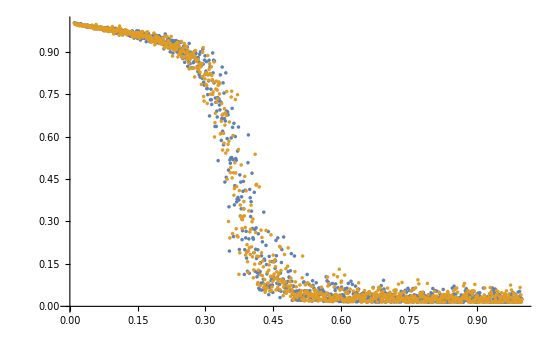

```mathematica
ListPlot[{Transpose[{xcyc,ycyc}],Transpose[{xcyc2,ycyc2}]},PlotRange->All]
```

```mathematica
(*converge it*)
```

```mathematica
(*midv[vv_]:=Sort[vv][[(Length[vv]+1)/2]];*)
```

```mathematica
(*lengthv=3980;sepv=10;
xcycC=Table[0,{i,1,lengthv/sepv}];
ycycC=Table[0,{i,1,lengthv/sepv}];
For[i=1,i≤(lengthv/sepv),i++,
tptx=Table[0,{i,1,sepv+1}];
tpty=Table[0,{i,1,sepv+1}];
For[j=1,j≤sepv+1,j++,
tptx[[j]]=xcyc[[(i-1)*sepv+j]];
tpty[[j]]=ycyc[[(i-1)*sepv+j]];
];
xcycC[[i]]=midv[tptx];
ycycC[[i]]=midv[tpty];
];*)
```

```mathematica
z6x={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.09999999,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.9899999,1,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2,2.01,2.02,2.03,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.26,2.27,2.28,2.29,2.3,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.51,2.52,2.53,2.54,2.55,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.76,2.77,2.78,2.79,2.8,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3,3.01,3.02,3.03,3.04,3.05,3.06,3.07,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.26,3.27,3.28,3.29,3.3,3.31,3.32,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5};
z6y={0.9986643,0.9991879,0.9967476,0.9963858,0.9953547,0.993864,0.9908482,0.9909819,0.9883015,0.9885921,0.9810129,0.98182,0.9833508,0.9813288,0.9847441,0.9788793,0.975488,0.9724319,0.9789043,0.970768,0.9766892,0.9729777,0.9667423,0.9671534,0.9697956,0.9759997,0.9678323,0.9613762,0.9690323,0.9698258,0.9616796,0.970262,0.9576867,0.9677801,0.9644556,0.9667741,0.9454992,0.9634016,0.9544373,0.9468836,0.9447672,0.9575324,0.9481166,0.9389873,0.9527456,0.9455911,0.9387643,0.9458011,0.9460117,0.9470556,0.9380536,0.9386598,0.9466501,0.9348583,0.9246183,0.9407521,0.9408966,0.9350112,0.9290088,0.9352477,0.9439741,0.9143832,0.9183969,0.9321652,0.9164976,0.931437,0.9097267,0.9118693,0.9071766,0.9179075,0.9194682,0.9054855,0.8925579,0.9048524,0.8967283,0.8972929,0.9012019,0.9091158,0.9105453,0.9006628,0.8663998,0.8817531,0.8970482,0.8708893,0.8490502,0.8596595,0.8471931,0.86019,0.8741202,0.8750876,0.8613564,0.813619,0.8310101,0.8082278,0.8535653,0.841012,0.8418836,0.8389373,0.8346807,0.8483098,0.8187698,0.8460861,0.777274,0.7961707,0.835243,0.7826353,0.7931102,0.7545949,0.7611927,0.7854761,0.6929728,0.7503478,0.7649618,0.6153554,0.7165085,0.7768146,0.6421089,0.7293213,0.6482798,0.6987258,0.5716016,0.7101489,0.6653236,0.583822,0.6046259,0.5892739,0.5674368,0.6022953,0.6124386,0.6332,0.5449225,0.6132883,0.6336312,0.5957618,0.5299528,0.5173504,0.5557331,0.5984371,0.5034201,0.4689541,0.5926899,0.3201506,0.5086605,0.5054501,0.4439374,0.4702886,0.5782948,0.5418018,0.45443,0.5310575,0.3150312,0.4699651,0.3543098,0.4850267,0.3271697,0.2675508,0.2904422,0.4314995,0.5138609,0.4064078,0.496172,0.4433329,0.4798337,0.3861557,0.4347275,0.1385482,0.1990094,0.4283772,0.5175222,0.2870381,0.5460437,0.3614188,0.5437221,0.4713019,0.2502456,0.1909044,0.2459917,0.1002172,0.2012565,0.4885522,0.5066198,0.4388945,0.1082524,0.2747028,0.1085128,0.2636713,0.2456636,0.3526319,0.2321942,0.3724371,0.3188062,0.05395139,0.08744311,0.3668774,0.3540658,0.3215079,0.3135084,0.5295599,0.3301071,0.1362591,0.04051933,0.05525257,0.3258458,0.03115077,0.02975511,0.1636522,0.2280181,0.01651111,0.01477242,0.2032662,0.2254188,0.2826435,0.232748,0.2728111,0.4935105,0.1982386,0.1084776,0.04141534,0.3284159,0.3485824,0.4517204,0.2438991,0.2338052,0.2279075,0.09936668,0.06582534,0.2251947,0.3230276,0.03046476,0.04926331,0.04806126,0.02864356,0.2128558,0.22656,0.4405828,0.1801982,0.2862617,0.3355757,0.2769924,0.1924822,0.03222544,0.1919791,0.1950663,0.2888447,0.08743057,0.2543573,0.1668216,0.2607449,0.1999478,0.02837997,0.1897871,0.2942774,0.2046165,0.2418196,0.1713124,0.3427763,0.287065,0.2269528,0.09522196,0.03116408,0.218731,0.2779558,0.2170326,0.08974116,0.1992007,0.1761654,0.1837129,0.449926,0.2637438,0.0632459,0.1980736,0.2850991,0.2496207,0.01044915,0.2094374,0.2490358,0.2142128,0.1647507,0.169273,0.2400934,0.418901,0.3256361,0.2583743,0.2011176,0.2220382,0.069897,0.1593886,0.3522004,0.2424855,0.2743899,0.1444269,0.2266342,0.1985723,0.186956,0.197951,0.07754038,0.1370896,0.1299972,0.130338,0.1530965,0.1977159,0.218458,0.01883163,0.01193116,0.0391284,0.1548592,0.1661001,0.2054638,0.1912861,0.1898135,0.1509032,0.1615349,0.2288847,0.0118776,0.1496759,0.1535962,0.01004619,0.009934888,0.009931318,0.009979418,0.05723099,0.06999092,0.07002095,0.1600552,0.1725701,0.148025,0.178844,0.1678161,0.01009267,0.1277187,0.1789674,0.1577439,0.2624141,0.1844599,0.2017634,0.1818178,0.2006994,0.1407172,0.1451025,0.1601416,0.1935743,0.1458051,0.2194319,0.1045676,0.1212225,0.1696063,0.01165607,0.00988339,0.02031373,0.1816256};
```

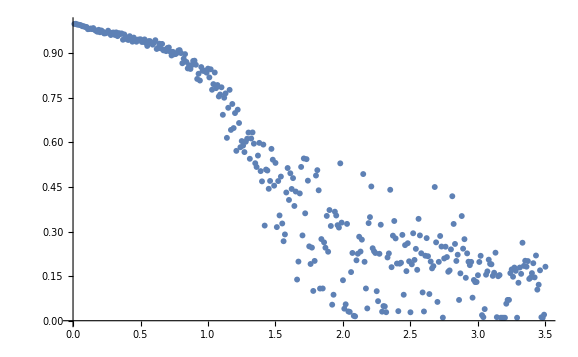

```mathematica
ListPlot[Transpose[{z6x,z6y}],PlotRange->All]
```

```mathematica
z2crit={0.02306366,0.04562378,0.4466934,0.1509399,0.129364,0.08914185,0.3555069,0.02831268,0.02475739,0.02577972,0.02502441,0.3520305,0.03990173,0.02799988,0.3497772,0.05036163,0.04375458,0.02613831,0.02553558,0.04711914,0.03153992,0.02506256,0.02310944,0.3527908,0.04165649,0.02355194,0.02284241,0.02574921,0.02671051,0.3525798,0.8584544,0.7960409,1.03879,0.4221242,0.06439972,0.03030396,0.02398682,0.04618835,0.04832458,0.3653158,0.04228973,0.02724457,0.02993774,0.03423309,0.03018951,0.03239441,0.03305817,0.03341675,0.3617757,0.03327942,0.352773,0.04962158,0.03742981,0.0269928,0.02600861,0.02364349,0.02541351,0.02446747,0.02233887,0.02327728,0.02529144,0.03112793,0.02640533,0.03671265,0.08499146,0.1142654,0.04853058,0.02802277,0.02710724,0.02719116,0.02598572,0.02558899,0.02394867,0.02334595,0.0272522,0.3566411,0.04179382,0.04483795,0.04113007,0.03079224,0.02867889,0.02701569,0.02400208,0.02952576,0.03031158,0.02445221,0.02462006,0.02340698,0.02514648,0.3549016,0.07862854,0.02759552,0.02552032,0.02418518,0.02485657,0.02611542,0.02347565,0.02403259,0.02735138,0.03381348,0.02693176,0.03138733,0.02576447,0.02599335,0.02534485,0.02455902,0.1344833,0.3858083,0.04733276,0.03055573,0.02520752,0.0249176,0.02454376,0.02329254,0.02467346,0.02791595,0.02664948,0.3504588,0.03839874,0.3587392,0.04464722,0.04967499,0.03295135,0.02636719,0.02307892,0.02409363,0.02664948,0.02471924,0.03155518,0.05656433,0.1062393,0.2117691,0.9920095,0.4453125,0.08267212,0.02849579,0.3576711,0.6773784,0.6477484,0.7400818,0.7327474,0.07717133,0.04082489,0.03892517,0.04058838,0.03771973,0.03520203,0.02713013,0.3528595,0.03251648,0.02986145,0.03266907,0.02398682,0.02425385,0.02445984,0.02657318,0.02771759,0.02681732,0.0326004,0.02579498,0.0425415,0.03508759,0.3525772,0.02804565,0.02592468,0.02709961,0.3559291,0.03730011,0.02598572,0.02601624,0.02944183,0.02748108,0.02687836,0.02716827,0.02622223,0.02667236,0.0254364,0.02476501,0.02452087,0.02439117,0.02527618,0.02321625,0.7927297,0.6963323,0.7452393,0.1609955,0.0631485,0.02711487,0.02466583,0.02389526,0.02416229,0.02655792,0.02616882,0.3530172,0.03541565,0.3553391,0.04154968,0.02810669,0.3488973,0.03617859,0.03572845,0.8567225,0.657369,0.4077174,0.073349,0.03297424,0.02442169,0.02456665,0.03445435,0.03017426,0.02605438,0.025383,0.3513082,0.03361511,0.02490234,0.352773,0.03883362,0.02531433,0.02419281,0.02752686,0.02549744,0.02713776,0.03049469,0.03411102,0.02890015,0.03009033,0.0428009,0.03497314,0.3552704,0.04164886,0.02526093,0.02572632,0.02407837,0.02870941,0.02613831,0.02514648,0.04111481,0.05256653,0.02470398,0.02507782,0.02674103,0.02615356,0.05046082,0.04038239,0.0318985,0.02906036,0.02568054,0.02442169,0.02554321,0.02635956,0.03651428,0.03217316,0.0266571,0.02763367,0.0245285,0.3517609,0.04971313,0.03869629,0.02947998,0.8835144,0.5469767,0.7156881,0.7720261,0.5385539,0.4815216,0.493604,1.309812,1.188405,0.875061,1.030088,0.9122264,0.8737056,0.9512762,0.5335693,0.5442123,0.5336609,0.7726364,0.9806646,0.7667389,0.9014893,0.9085236,0.5681814,0.4360428,0.1048355,0.3573278,0.03083038,0.02722931,0.02680969,0.02381134,0.0236969,0.0231781,0.02440643,0.0241394,0.02388763,0.02722168,0.02469635,0.02404022,0.356837,0.04129028,0.02736664,0.0246048,0.02470398,0.02361298,0.02402496,0.02618408,0.3504995,0.3733419,0.04999542,0.03513336,0.04450989,0.03953552,0.02696991,0.04084015,0.03314209,0.02754974,0.02497101,0.02490997,0.02524567,0.02294159,0.02610016,0.02555847,0.03031158,0.4245479,0.4287084,0.4897919,0.9370906,0.5810369,0.504069,0.06170654,0.03297424,0.02597809,0.02513885,0.02542877,0.02481079,0.03022766,0.03033447,0.02565765,0.02391815,0.02919006,0.03089905,0.04644012,0.3644994,0.05121613,0.360433,0.3895925,0.5293223,0.4871114,0.1919327,0.1138,0.3852946,0.3761546,0.08687592,0.03639984,0.6926753,0.4854558,0.1013641,0.04951477,0.03755188,0.02828217,0.02823639,0.02481842,0.0252533,0.02670288,0.04036713,0.03344727,0.02416992,0.02419281,0.02427673,0.02437592,0.02412415,0.02479553,0.02581787,0.0240097,0.02449799,0.0247879,0.04315948,0.02738953,0.02857208,0.0350647,0.02935791,0.02748108,0.0246048,0.02375031,0.9934108,0.414622,0.09539795,0.03039551,0.108017,0.7442449,0.2751389,0.09739685,0.02910614,0.02432251,0.04627228,0.04502869,0.03412628,0.02306366,0.02422333,0.02644348,0.03408051,0.02906799,0.02642059,0.024086,0.03202057,0.3596751,0.03925323,0.02565765,0.03157043,0.3567556,0.04432678,0.0386734,0.03257751,0.02468109,0.02462006,0.03137207,0.02700806,0.3534266,0.04264832,0.3635483,0.04485321,0.03049469,0.02561188,0.02446747,0.0238266,0.02309418,0.02409363,0.02364349,0.02372742,0.02978516,0.02511597,0.02561188,0.02374268,0.3515701,0.03155518,0.02550507,0.3494263,0.04177856,0.03221893,0.02445221,0.03366852,0.3595225,0.0440979,0.02924347,0.02554321,0.02674866,0.02601624,0.02677155,0.03349304,0.05299377,0.06812286,0.04580688,0.03166962,0.02494812,0.02497864,0.02532959,0.02509308,0.3631744,0.112915,0.05556488,0.03587341,0.03005219,0.02510834,0.02318573,0.02381134,0.0243988,0.02555847,0.02494049,0.02476501,0.02987671,0.0243988,0.02540588,0.02603149,0.3756739,0.9247513,1.107979,0.5054016,0.4588598,0.09042358,0.03385925,0.02631378,0.02497101,0.02599335,0.02526093,0.02346039,0.02692413,0.02568054,0.02807617,0.03466034,0.02427673,0.02311707,0.02303314,0.03892517,0.02489471,0.02365875,0.02420807,0.0243988,0.03171539,0.02615356,0.0251236,0.02383423};
```

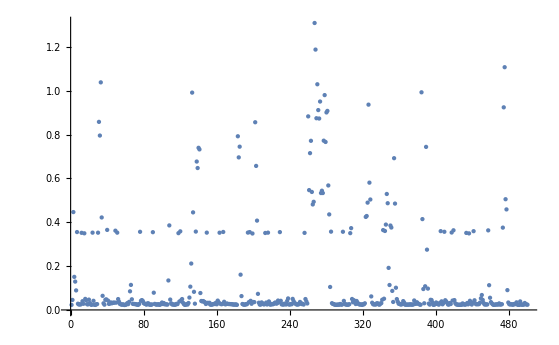

```mathematica
ListPlot[z2crit,PlotRange->All]
```

```mathematica
z6crit={0.3631223,0.3317655,0.4523087,0.4331544,0.6830673,0.3566888,0.3995737,0.2467734,0.7278398,0.770045,0.9401843,0.9423186,1.031293,0.8575472,0.8626055,0.8005193,0.7994112,0.6145458,0.6673336,0.6788038,0.7662722,0.881705,0.799333,0.7578036,0.9598802,0.848685,0.8670152,0.9744937,1.121138,0.7164828,0.775692,1.009873,0.78062,0.7431545,0.9879074,0.8696048,1.043959,0.9257565,1.097407,0.7899584,0.9495081,0.7662659,0.858724,0.7714202,0.8130054,0.9854412,0.7345899,0.7624416,0.8573374,0.9462077,0.9089171,0.8438594,0.8198318,0.8560696,0.9819133,0.8821341,0.9077524,0.5253665,0.7068481,0.5957369,0.8658333,0.9561927,0.9125303,0.9389712,0.6459446,0.4098504,0.4220664,0.3729948,0.7042269,0.5978107,0.8127435,0.7878609,0.5200526,1.041578,0.7614988,0.5562649,0.5485096,0.5600719,0.4116949,0.4078566,0.4307245,0.442332,0.7485657,0.8388799,0.6401431,0.7992179,0.8965588,0.7300987,0.5014286,0.5978127,0.7006989,0.4627228,0.4228147,0.6120733,0.4960378,0.5433471,0.9461238,0.9446234,0.9781609,0.8918457,0.8682359,1.043851,0.8241889,0.8879547,0.9123898,0.9352793,0.8176906,0.9252638,0.8951365,0.9178804,0.9272976,0.8587227,1.021711,0.7236513,0.9512431,0.6731224,0.736145,0.7846235,0.8231913,0.8450642,0.9968631,1.0676,1.099089,0.8742861,0.8968824,1.052485,0.9522426,0.7950675,0.8113174,0.8321146,0.9311943,0.7472242,0.8510577,1.034639,0.8816204,0.8878574,0.8020954,0.7755032,0.6905308,0.8279139,0.9607627,0.9014778,0.8111426,0.8834146,0.9658426,0.8963369,0.912131,0.8863939,0.8858942,0.7617232,0.8960533,0.840587,0.7598795,0.7097651,1.22093,0.894811,0.7115371,0.8928522,0.8696836,0.9173464,0.8978462,1.033537,0.9837901,0.8240942,0.8197365,1.089788,0.819334,0.7505627,0.768048,0.7019806,0.9136181,0.891587,0.7876365,0.8750114,0.6102263,0.9591408,0.9607296,0.8261732,0.6035048,0.5656389,0.7130274,0.7638168,0.8827642,1.016032,0.8947532,0.9218553,0.9933726,0.9337444,1.009262,0.7406502,1.033473,0.8515841,1.001287,0.8558814,1.041122,0.5540397,0.6881263,0.8114917,0.8984585,0.9880199,0.9237118,0.9400482,0.8695291,0.9986515,0.7020582,0.9909281,0.8076509,0.7849159,0.7521147,0.6111183,0.6261228,0.8874531,0.8197174,0.7493433,0.783048,1.026157,0.7733721,0.8203405,0.8280036,0.964435,1.23193,0.9848614,0.8613936,0.9132831,0.9253928,0.9105708,0.7561735,0.6049093,0.578963,0.730884,0.7354832,0.7985491,1.008867,0.855842,0.9349028,0.7848358,0.8144506,0.8113899,0.8499864,0.9108194,0.8592746,0.9663582,0.8631872,0.5443968,0.5056928,0.9616197,1.088873,0.8060195,0.7708232,0.8385665,0.896307,0.9360956,0.857598,1.007622,0.7706064,0.8753484,0.6882,0.4804656,0.6699371,0.6496296,0.6713511,0.4938838,0.6181717,0.97892,0.6634998,0.9081339,0.617433,0.7989826,0.8314063,0.8355389,0.7561423,0.8345623,0.7598636,0.8265693,0.8498001,1.063097,0.8674068,0.9001058,0.9499251,0.9640503,0.9841678,0.809824,1.111364,0.914451,0.9181353,0.792525,0.7728888,0.9344267,0.927447,0.969319,0.9823863,0.7905871,0.9748949,0.9573752,0.981191,0.9779505,0.8645077,0.8635877,1.039478,0.9058158,0.8708922,0.6690801,0.9307124,0.8951397,0.974631,0.6719017,0.6456999,0.5725734,0.7123572,0.5575148,0.7983043,0.9590995,0.9662679,0.8338909,0.8138123,0.8876356,0.7300269,0.6988093,0.6296762,0.6084563,0.3704446,0.518186,0.4710662,0.8186385,1.022408,0.8317661,0.9464239,1.069174,0.8830147,0.6796507,0.8450407,0.909586,0.718195,0.5966937,0.7032871,0.998216,1.019669,0.9372622,0.8948269,0.9284064,0.8160414,0.8875186,0.7584356,0.7945372,0.591212,0.4137961,0.5146288,0.6521587,0.5986252,0.536665,0.4917342,0.7056103,0.8398813,0.7442672,0.8220743,1.045813,0.962314,1.047647,0.7459043,0.6195196,0.6294498,0.8649267,0.8018049,0.7683182,0.839489,0.9063568,0.8622386,0.8528976,0.7924436,0.6987788,0.8162944,0.891201,1.011026,0.8440482,0.9147568,0.7329878,0.9621391,0.6402391,0.9001598,0.7670364,0.53744,0.6146622,0.5563037,0.4725348,0.7957789,1.106314,0.7810428,0.6586126,1.124721,0.9238701,1.176243,0.9334227,0.9002355,0.9379877,0.85919,0.6364664,0.9554342,0.9404075,0.8715159,0.576589,0.514604,0.5123584,0.4430097,0.8219179,0.6212985,0.8669605,0.835797,0.9308288,0.9159616,0.9334323,0.9213728,0.783514,0.7574756,0.5932166,0.7502677,0.8800462,0.9100768,0.9733658,0.7998003,0.8720659,0.8917491,0.8695501,0.7784144,0.7299728,0.9170418,0.9142132,0.7921003,0.7140681,0.6589546,0.7735761,0.7935804,1.011738,0.6459758,0.7608795,0.8554427,0.7582296,0.7190425,0.6965815,0.6512229,0.9061108,0.8315233,0.8391444,1.073513,0.9646168,0.634407,1.014627,0.8969816,0.9448293,1.010918,1.038986,0.958877,0.7772421,0.5168566,0.9075407,0.7822018,0.7945118,0.8175882,0.8735689,0.8103861,1.103498,0.9099706,0.7170982,0.7971026,1.083937,0.9000626,0.8337237,0.9921703,0.745437,0.8278351,0.5891699,0.8717022,0.8522409,0.6648064,0.7949175,0.6556625,0.804561,0.936615,1.062578,0.9091587,0.9127611,0.9897722,0.8308487,1.120007,0.9179713,0.5872065,0.6901417,0.8253174,0.8603103,0.7499899,1.033664,0.8317204,0.8397001,1.00145,0.9195105,0.7994798,0.6281853,0.599947,0.9564947,0.9211935,0.7181925};
```

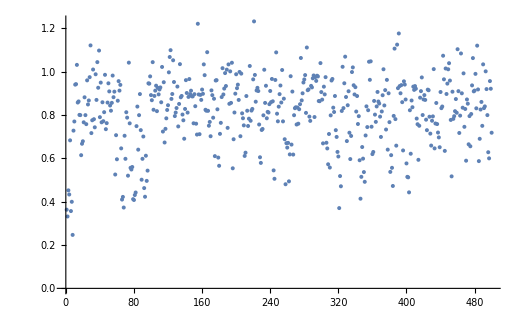

```mathematica
ListPlot[z6crit,PlotRange->All]
```

```mathematica
(*4X4X4 lattice*)
```

```mathematica
x3dz2={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.09999999,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.9899999,1};
y3dz2={0.9663965,0.9600292,0.9503393,0.952208,0.9264951,0.9194351,0.8994673,0.8753457,0.8340946,0.7428712,0.7122784,0.6813747,0.6722729,0.6155521,0.608112,0.5180647,0.5149848,0.4973009,0.474183,0.4695113,0.3830981,0.384863,0.3745847,0.3445458,0.336621,0.2984843,0.2724253,0.2583749,0.2379569,0.2458472,0.249031,0.1682932,0.1694699,0.1810286,0.1812016,0.1148602,0.152201,0.1387043,0.1252422,0.135209,0.1377007,0.1309524,0.09603406,0.09243494,0.07468165,0.06357287,0.07104789,0.07381645,0.05886629,0.04959165,0.0660991,0.05180646,0.02792776,0.04017855,0.03595652,0.03066168,0.04222037,0.03696018,0.0267165,0.02021041,0.02713179,0.0367525,0.02197534,0.01612679,0.01920682,0.01550387,0.01609218,0.01841084,0.01948366,0.01460409,0.01481174,0.01574613,0.01481173,0.01218162,0.01574611,0.0130814,0.01290837,0.01245848,0.01072813,0.01546926,0.01408499,0.01294297,0.0110742,0.0105205,0.01142027,0.008271043,0.01263151,0.01377354,0.01605758,0.01086656,0.01238926,0.009862959,0.0136005,0.008582504,0.01280454,0.0105897,0.01124723,0.01349669,0.01363511,0.01173174};
```

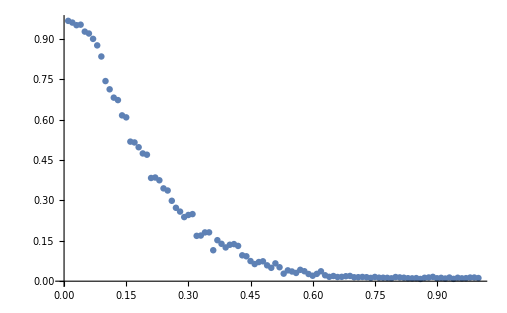

```mathematica
ListPlot[Transpose[{x3dz2,y3dz2}],PlotRange->All]
```

```mathematica
x3dz4={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.09999999,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.9899999,1,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2};
y3dz4={0.9764849,0.9828867,0.9755329,0.9693556,0.9540246,0.9529348,0.9515329,0.951983,0.9577796,0.9518442,0.9409086,0.9297827,0.9091742,0.9116145,0.8599808,0.8771973,0.83868,0.8526438,0.8633373,0.8326927,0.8240065,0.8160472,0.7085233,0.682932,0.6307102,0.642615,0.5970722,0.6534296,0.5373237,0.6393445,0.5760487,0.5614967,0.5523602,0.6101707,0.5272529,0.5352126,0.4683348,0.4756715,0.4798935,0.4587658,0.460652,0.4411166,0.4167185,0.4115622,0.3767477,0.3581983,0.3985326,0.3858494,0.3449093,0.3460858,0.3012353,0.3099908,0.320944,0.269051,0.2889501,0.276855,0.2623892,0.2779797,0.2546719,0.2161718,0.1903204,0.2091465,0.2196497,0.173242,0.1766334,0.1727574,0.2012908,0.1703351,0.1841085,0.1669781,0.1689681,0.1321983,0.1524952,0.1567518,0.1441203,0.1217989,0.1292047,0.1198955,0.1060354,0.1351571,0.1137009,0.1504533,0.109773,0.1201723,0.08324683,0.07824615,0.09035847,0.0866729,0.07746744,0.072709,0.0776751,0.08904346,0.07689649,0.07961308,0.08433691,0.05884898,0.05630537,0.05800113,0.08693242,0.04708263,0.05462695,0.05082018,0.07385104,0.05730898,0.04318938,0.04905524,0.04031699,0.0448159,0.05672064,0.04317209,0.04355275,0.05632269,0.04142444,0.04872645,0.04043812,0.0488303,0.02538413,0.02920819,0.02550525,0.02810079,0.02746055,0.02505537,0.02346346,0.02405178,0.02664729,0.02398255,0.02057378,0.02055647,0.01886074,0.02088525,0.0232385,0.02252908,0.0196567,0.02104099,0.01984704,0.02104097,0.01934524,0.01912029,0.02491694,0.0211794,0.01979512,0.01654208,0.01834164,0.01996815,0.01609218,0.01695736,0.01323712,0.01583264,0.01527893,0.01527893,0.01330634,0.01657669,0.01496747,0.01475983,0.01097037,0.01493286,0.009084301,0.01247578,0.01583264,0.01136835,0.01356589,0.01294297,0.01301218,0.01292566,0.0115587,0.01199128,0.01221622,0.009966769,0.01122993,0.01548658,0.01629983,0.0131333,0.01238926,0.0126488,0.01432726,0.01280454,0.01320252,0.01716501,0.0141196,0.01500207,0.01084925,0.01308139,0.01116071,0.01418881,0.01380814,0.01181824,0.01147217,0.01482906,0.01204319,0.01283915,0.01347937,0.01225083,0.01031284,0.01401577,0.01280454,0.012147,0.01290836,0.01510591,0.01370432,0.01505399};
```

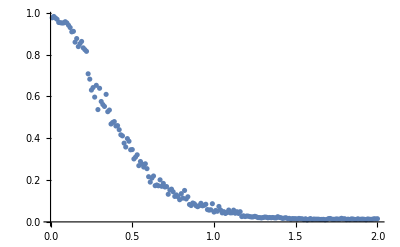

```mathematica
ListPlot[Transpose[{x3dz4,y3dz4}],PlotRange->All]
```